Yohan Lee Lab 7

Examples

```mathematica
Table[Sqrt[i], {i,1,10}]//N
```

{1.,1.41421,1.73205,2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228}

```mathematica
Table[Sqrt[i], {i,1,10}]//TableForm//N
```

1.
1.41421
1.73205
2.
2.23607
2.44949
2.64575
2.82843
3.
3.16228

```mathematica
a[n_]:=(3n^2-(-1)^n+n)/(7n^2-6n+4);
```

```mathematica
seq=Table[{n,a[n]},{n,1,101}]//N;
seq[[;; ;; 10]]//TableForm
```

1. | 1.
11. | 0.477707
21. | 0.453626
31. | 0.445378
41. | 0.441215
51. | 0.438704
61. | 0.437026
71. | 0.435824
81. | 0.434921
91. | 0.434219
101. | 0.433656

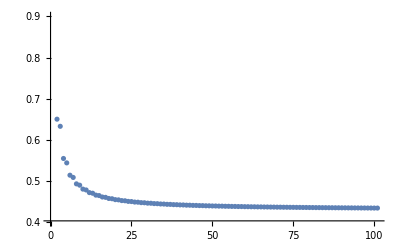

```mathematica
ListPlot[seq,PlotRange->{.4,.9}]
```

```mathematica
Limit[a[n], n->Infinity]//N
```

0.428571

Question 1

```mathematica
b[n_]=(2+(-1)^n*n^2)/(n^2-3n+4);
```

```mathematica
b[n]
```

(2+(-1)^n n^2)/(4-3 n+n^2)

```mathematica
seq=Table[{n,b[n]},{n,1,101}]//N;
seq[[;; ;; 10]]//TableForm
```

1. | 0.5
11. | -1.29348
21. | -1.14921
31. | -1.09977
41. | -1.0749
51. | -1.05995
61. | -1.04997
71. | -1.04284
81. | -1.03749
91. | -1.03333
101. | -1.02999

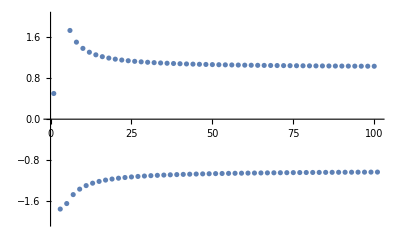

```mathematica
ListPlot[seq,PlotRange->{-2,2}]
```

```mathematica
Limit[b[n], n->Infinity]//N
```

2.71828^((0.+2. ⅈ) Interval[{-2.22507×10^-308,3.14159}])

Limit DNE because elements of seq approach a number but alternate in sign.

Question 2

```mathematica
c[n_]:=Log[n]/n^(1/3)
```

```mathematica
Function[n,Log[n]/n^(1/3)]
```

Function[n,Log[n]/n^(1/3)]

```mathematica
seq=Table[{n,c[n]},{n,1,101}]//N;
seq[[;; ;; 5]]//TableForm
```

1. | 0.
6. | 0.986043
11. | 1.0782
16. | 1.1003
21. | 1.10352
26. | 1.09978
31. | 1.09315
36. | 1.08528
41. | 1.07695
46. | 1.06854
51. | 1.06024
56. | 1.05214
61. | 1.0443
66. | 1.03673
71. | 1.02943
76. | 1.02241
81. | 1.01565
86. | 1.00914
91. | 1.00287
96. | 0.996831
101. | 0.991005

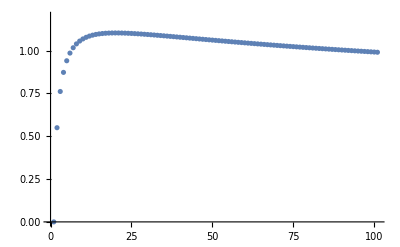

```mathematica
ListPlot[seq,PlotRange->{0,1.2}]
```

```mathematica
Limit[c[n], n->Infinity]//N
```

0.

Limit exists as the sequence converges to 0.

Question 3

```mathematica
d[n_]:=Sin[Tan[Sqrt[n^2-n]]]
```

```mathematica
Function[n,Sin[Tan[√(n^2-n)]]]
```

Function[n,Sin[Tan[√(n^2-n)]]]

```mathematica
seq=Table[{n,d[n]},{n,1,1001}]//N;
seq[[;; ;; 71]]//TableForm
```

1. | 0.
72. | -0.811884
143. | 0.860248
214. | -0.129242
285. | 0.814655
356. | 0.519175
427. | -0.810237
498. | 0.858423
569. | -0.128843
640. | 0.819297
711. | 0.519403
782. | -0.810056
853. | 0.858045
924. | -0.128727
995. | 0.820974

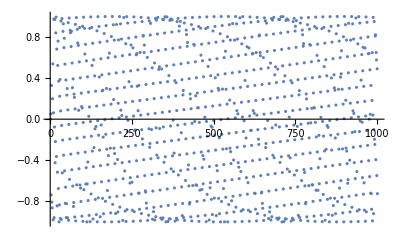

```mathematica
ListPlot[seq,PlotRange->{2,-2}]
```

```mathematica
Limit[d[n], n->Infinity]//N
```

Limit[Sin[Tan[√(-1. n+n^2)]],n→∞]

The sequence does not converge to a number so the limit DNE.

Question 4

```mathematica
f[n_]:=((-1)^(n+1)*Factorial[2n+1])/(4^(2n+3)*Factorial[n+2]*Factorial[n])
```

```mathematica
Function[n,((-1)^(n+1) (2 n+1)!)/(4^(2 n+3) (n+2)! n!)]
```

Function[n,((-1)^(n+1) (2 n+1)!)/(4^(2 n+3) (n+2)! n!)]

```mathematica
seq=Table[{n,f[n]},{n,1,101}]//N;
seq[[;; ;; 7]]//TableForm
```

1. | 0.000976563
8. | -8.84393×10^-9
15. | 2.39593×10^-13
22. | -8.66004×10^-18
29. | 3.5876×10^-22
36. | -1.60977×10^-26
43. | 7.61242×10^-31
50. | -3.73614×10^-35
57. | 1.88518×10^-39
64. | -9.71851×10^-44
71. | 5.09651×10^-48
78. | -2.71022×10^-52
85. | 1.45806×10^-56
92. | -7.92142×10^-61
99. | 4.33982×10^-65

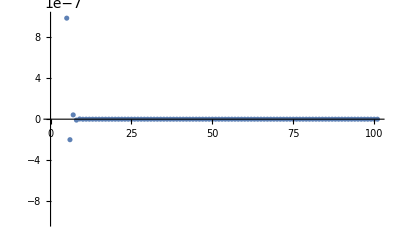

```mathematica
ListPlot[seq,PlotRange->{-.000001,.000001}]
```

```mathematica
Limit[f[n], n->Infinity]//N
```

0.

Limit exists as the sequence converges to 0.

```mathematica
13/8+Sum[f[n], {n,0,Infinity}]
```

13/8+1/8 (-9+4 √5)

```mathematica
13/8+Sum[f[n], {n,0,Infinity}]//N
```

1.61803

The above expression has a finite sum as expected as the sequence converges to 0.